```mathematica
(*Define Directions*)
xhat = {1,0};
yhat = {0,1};
thetahat = {1,0};
rhat = {0,1};

(*some nice helper functions*)
polarToCartesian[Θ_,R_]={R Cos[Θ],R Sin[Θ]};
rotToGrav[omega_,r_] = r*(omega^2);
cartesianToPolar[x_,y_] = {ArcTan[x,y],Sqrt[x^2 + y^2]};

(*Define functions for different projectile motions*)
(*arclength equation*)
arcLengthProjectileMotion[t_,v0_,ΘThrow_,Θinit_,r0_,omega_,R_] = Module[{
(*Define Local variables*)
refPointOnShip, startPointOnShip,projectilePath,initProjectileVelocity
},
refPointOnShip =  R{Cos[omega*t+Θinit],Sin[omega *t +Θinit]};
startPointOnShip =  r0{Cos[Θinit],Sin[Θinit]};
initProjectileVelocity = {v0 Cos[ΘThrow + Pi/2 +Θinit ],v0 Sin[ΘThrow + Pi/2 + Θinit]} +  r0*omega*{-Sin[Θinit],Cos[Θinit ]};
projectilePath = initProjectileVelocity * t +startPointOnShip;
{R*(ArcTan[xhat.projectilePath,yhat.projectilePath]-omega*t),R-Sqrt[projectilePath.projectilePath]}]



gravProjectileMotion [t_,v0_,Θ_,x0_,y0_,g_] = {
(*horizontal component*)
v0 t Cos[Θ]+x0,
(*vertical Component*)
-g/2*t^2 + v0 t Sin[Θ] + y0
};

arcLengthProjectileMotionL[t_,v0_,ΘThrow_,Θinit_,r0_,omega_,R_] ={-arcLengthProjectileMotion[t,v0,Pi-ΘThrow,Θinit,r0,omega,R].xhat,arcLengthProjectileMotion[t,v0,Pi-ΘThrow,Θinit,r0,omega,R].yhat}
```

{R (-omega t+ArcTan[r0 Cos[Θinit]+t (-omega r0 Sin[Θinit]-v0 Sin[Θinit+ΘThrow]),t (omega r0 Cos[Θinit]+v0 Cos[Θinit+ΘThrow])+r0 Sin[Θinit]]),R-√((t (omega r0 Cos[Θinit]+v0 Cos[Θinit+ΘThrow])+r0 Sin[Θinit])^2+(r0 Cos[Θinit]+t (-omega r0 Sin[Θinit]-v0 Sin[Θinit+ΘThrow]))^2)}

{-R (-omega t+ArcTan[r0 Cos[Θinit]+t (-omega r0 Sin[Θinit]+v0 Sin[Θinit-ΘThrow]),t (omega r0 Cos[Θinit]-v0 Cos[Θinit-ΘThrow])+r0 Sin[Θinit]]),R-√((t (omega r0 Cos[Θinit]-v0 Cos[Θinit-ΘThrow])+r0 Sin[Θinit])^2+(r0 Cos[Θinit]+t (-omega r0 Sin[Θinit]+v0 Sin[Θinit-ΘThrow]))^2)}

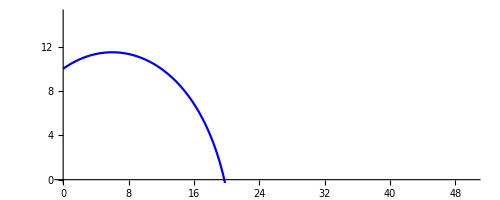

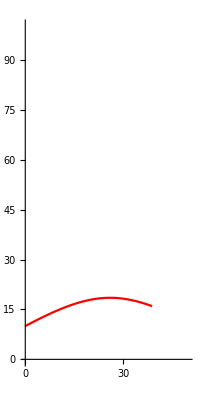

1.1

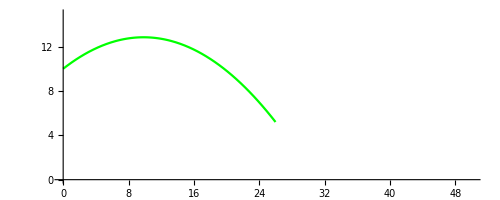

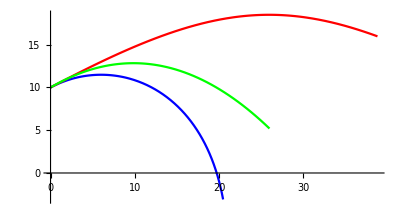

```mathematica
ArcLengthPlotRight = ParametricPlot[arcLengthProjectileMotion[t,5,Pi/6,0,100,.1,110],{t,0,5},PlotStyle->Blue,PlotRange->{{0,50},{0,15}}]
ArcLengthPlotLeft = ParametricPlot[arcLengthProjectileMotionL[t,5,Pi/6,0,100,.1,110],{t,0,10},PlotStyle->Red,PlotRange->{{0,50},{0,100}}]
equivGrav = rotToGrav[.1,110]
gravProjectileMotionPlot = ParametricPlot[gravProjectileMotion[t,5,Pi/6,0,10,equivGrav],{t,0,6},PlotStyle->Green,PlotRange->{{0,50},{0,15}}]
Show[ArcLengthPlotRight ,ArcLengthPlotLeft, gravProjectileMotionPlot,PlotRange->All,PlotRange->{{0,200},{0,15}}]
```

```mathematica
xi
```

xi

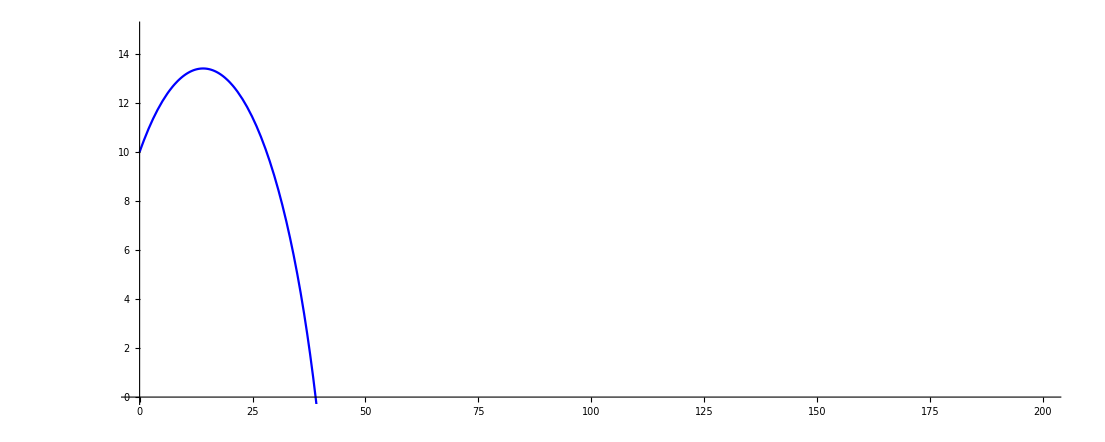

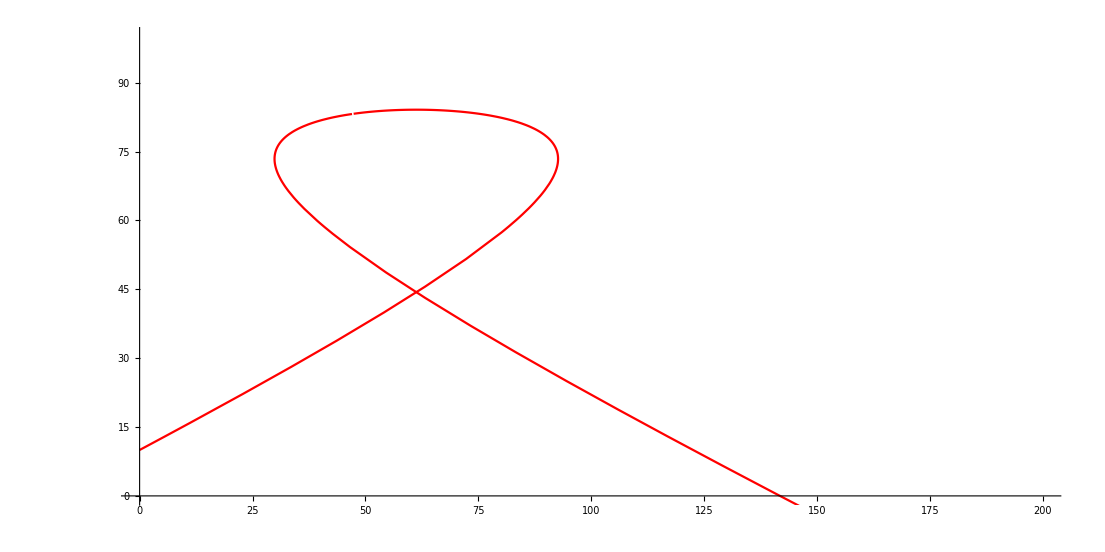

1.1

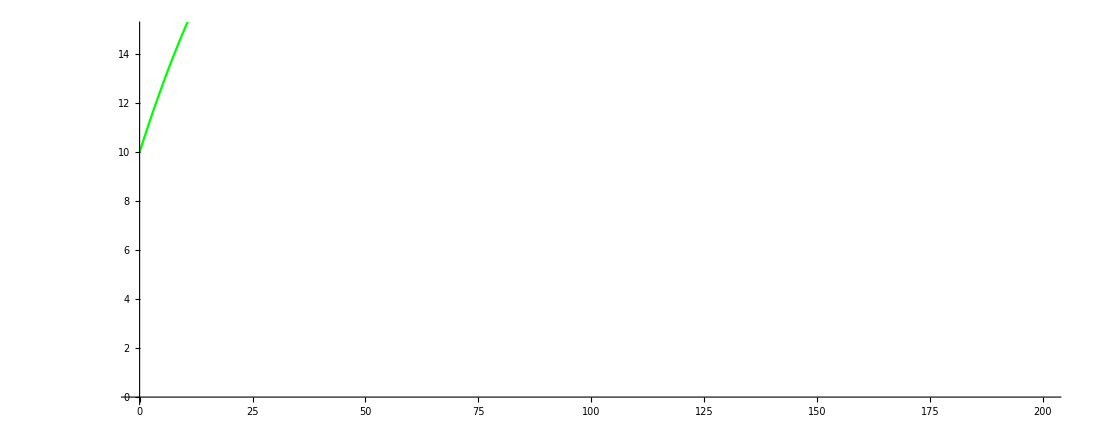

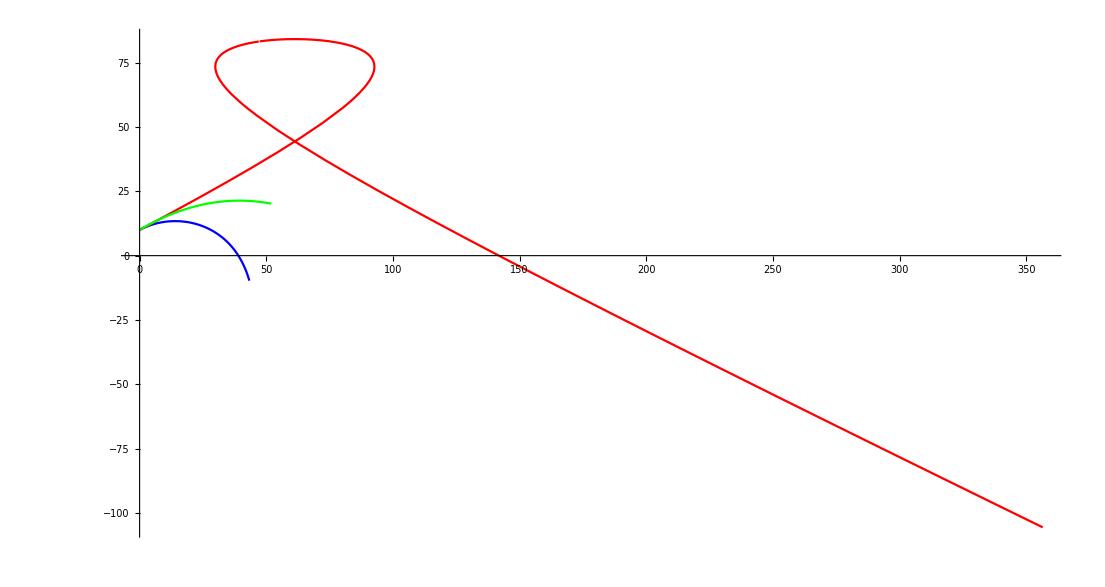

```mathematica
ArcLengthPlotRight = ParametricPlot[arcLengthProjectileMotion[t,10,Pi/6,0,100,.1,110],{t,0,5},PlotStyle->Blue,PlotRange->{{0,200},{0,15}}]
ArcLengthPlotLeft = ParametricPlot[arcLengthProjectileMotionL[t,10,Pi/6,0,100,.1,110],{t,0,60},PlotStyle->Red,PlotRange->{{0,200},{0,100}}]
equivGrav = rotToGrav[.1,110]
gravProjectileMotionPlot = ParametricPlot[gravProjectileMotion[t,10,Pi/6,0,10,equivGrav],{t,0,6},PlotStyle->Green,PlotRange->{{0,200},{0,15}}]
Show[ArcLengthPlotRight ,ArcLengthPlotLeft, gravProjectileMotionPlot,PlotRange->All,PlotRange->{{0,200},{0,15}}]
```

```mathematica
inertialPlotRight = ParametricPlot[Module[{arclen ,theta,radius},
arclen = arcLengthProjectileMotion[t,3,Pi/6,-Pi/2,100,.01,110];
theta =( arclen.thetahat)/110 ;
radius = -1*arclen.rhat + 110;
{radius Cos[theta],radius Sin[theta]
}],{t,0,40}];
inertialPlotLeft = ParametricPlot[Module[{arclen ,theta,radius},
arclen = arcLengthProjectileMotion[t,3,5Pi/6,-Pi/2,100,.01,110];
theta =( arclen.thetahat)/110 ;
radius = -1*arclen.rhat + 110;
{radius Cos[theta],radius Sin[theta]
}],{t,0,40}];
```

#### Heart

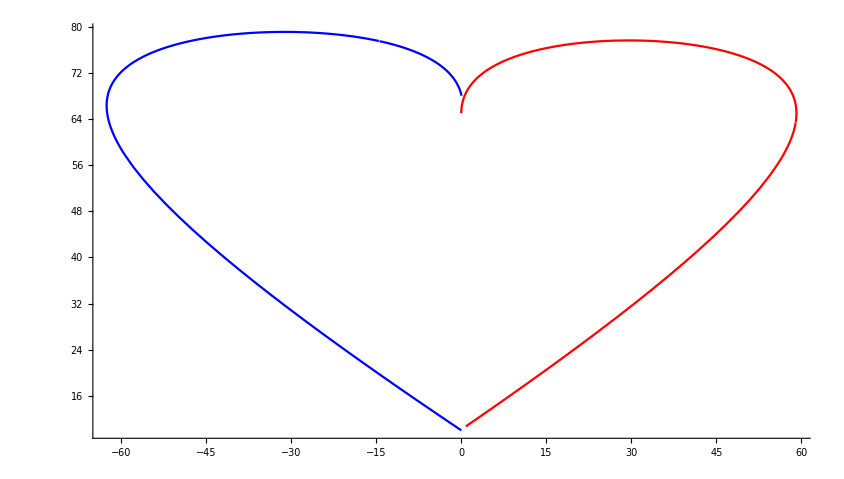

```mathematica
ArcLengthPlotRight = ParametricPlot[arcLengthProjectileMotion[t,10, (4.801 Pi)/6,0,100,.1,110],{t,0,20},PlotStyle->Blue,PlotRange->{{0,50},{0,15}}];
ArcLengthPlotLeft = ParametricPlot[arcLengthProjectileMotion[t,4.35,3Pi/6,0,45,.1,110],{t,0,20},PlotStyle->Red,PlotRange->{{0,50},{0,100}}];
Show[ArcLengthPlotRight ,ArcLengthPlotLeft,PlotRange->All,PlotRange->{{0,200},{0,15}}]
```

## Taylor Series Expansion

### Vertical Motion

```mathematica
verticalFormula = arcLengthProjectileMotion[t,V0,thetaThrow,-Pi/2,r,Sqrt[g/R],R].{0,1} //FullSimplify;
horizontalFormula =  arcLengthProjectileMotion[t,V0,thetaThrow,-Pi/2,R-h,omega,R].{1,0} //FullSimplify
horizontalFormula =R (-omega t + ArcTan[t (omega (-h+R)+V0 Cos[thetaThrow]),h-R+t V0 Sin[thetaThrow]]);
```

R (-omega t+ArcTan[t (omega (-h+R)+V0 Cos[thetaThrow]),h-R+t V0 Sin[thetaThrow]])

We investigate each term in the vertical equation of motion. We should expect the terms to match up with standard gravity in the limit that the radius is much bigger than the max height of the projectile. Since the path of the projectile can be described as a chord through a circle, the max height is just the point on the chord that is closest to the center of the ship. To find the chord, we get the secant line (http://mathworld.wolfram.com/Circle-LineIntersection.html) then we just find the midpoint between the two intersection points. On could construct a sort of toroid shaped ship with outer radius r2 and inner radius r1 to describe space in which ‘acceptable’ projectiles could fly through.

```mathematica
Series[verticalFormula,{t,0,0}]
```

(-√(r^2)+R)+O[t]^1

The second term of the series expansion for vertical motion corresponds to the term V_y*t.

```mathematica
SeriesCoefficient[verticalFormula,{t,0,1}]
```

(√(r^2) V0 Sin[thetaThrow])/r

The third term in the series corresponds to the term -1/2 g t^2 .

```mathematica
SeriesCoefficient[verticalFormula,{t,0,2}]
```

(-g r^2-2 r √(g/R) R V0 Cos[thetaThrow]-R V0^2 Cos[thetaThrow]^2)/(2 √(r^2) R)

#### Horizontal Motion

Now we compare gravitational horizontal motion to artificial gravity projectile horizontal motion. The equation of horizontal motion for gravitational projectiles has 2 terms: x0, V_x. We will look at the first 2 terms of the series to see how well they line up with gravitational projectile motion. We will look at the third term to also get a bettwe sense of how the artificial gravity differs from standard gravity. For the first term we find that the term is essentially zero since it evaluates to the logarithm of 1.

```mathematica
SeriesCoefficient[horizontalFormula,{t,0,0}]
```

-ⅈ R Log[(ⅈ (h-R))/(√((h-R)^2))]

For the Second Term we find that in the limit that the the height at which the ball is thrown is much smaller than the Radius of the ship, the artificial gravity term is essentially V_x.

```mathematica
FullSimplify[ExpToTrig[SeriesCoefficient[horizontalFormula,{t,0,1}]]]
```

(R V0 Cos[thetaThrow])/(-h+R)

For the Third Term we find that

```mathematica
FullSimplify[ExpToTrig[SeriesCoefficient[horizontalFormula,{t,0,2}]]]
```

(R V0 (omega (-h+R)+V0 Cos[thetaThrow]) Sin[thetaThrow])/(h-R)^2

```mathematica
FullSimplify[ExpToTrig[SeriesCoefficient[horizontalFormula,{t,0,3}]]]
```

1/3 R (-omega^3+(-3 omega (h-R) V0 (omega (-h+R) Cos[thetaThrow]+V0 Cos[2 thetaThrow])+V0^3 Cos[3 thetaThrow])/(h-R)^3)

```mathematica
1/3 R (-omega^3+(-3 omega (h-R) V0 (omega (-h+R) Cos[thetaThrow]+V0 Cos[2 thetaThrow])+V0^3 Cos[3 thetaThrow])/(h-R)^3)
```

1/3 R (-omega^3+(-3 omega (h-R) V0 (omega (-h+R) Cos[thetaThrow]+V0 Cos[2 thetaThrow])+V0^3 Cos[3 thetaThrow])/(h-R)^3)